```mathematica
(*********************************************)
Print[Style["Prove that sychronous gauge is special",Orange]]
(*********************************************)
```

Prove that sychronous gauge is special

```mathematica
(*********************************************)
Print[Style["Parameters",Orange]]
(*********************************************)
Subscript[w, 1]=-1;
Subscript[w, 2]=-0.25;
Subscript[w, 3]=-0.5;
Subscript[w, 4]=-0.75;
Subscript[Ω, DE0]=0.734;
Subscript[Ω, k0]=0;
Subscript[Ω, m0]=0.1334/(0.71^2);
Subscript[Ω, r0]=8.09*10^-5;
h=0.71;
H0=(100 h)/300000;
Subscript[Ω, m0,s]=1;Subscript[Ω, r0,s]=8.09*10^-5;
```

Parameters

0.000236667 √(0.734+0.0000809/x^4+0.26463/x^3)

0.000236667 √(0.734+0.0000809/a^4+0.26463/a^3) ∫_0^a (7.54377×10^10)/((0.734+0.0000809/x^4+0.26463/x^3)^(3/2) x^3)ⅆx

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.719399}. NIntegrate obtained 3.12984×10^12 + 4.18541×10^12\ ⅈ and 2.90742×10^12 for the integral and error estimates.

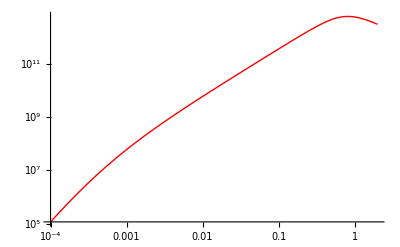

```mathematica
H[x_]=H0 √(Subscript[Ω, m0] x^-3+Subscript[Ω, r0] x^-4+Subscript[Ω, DE0])
δ[a_]=H[a] Integrate[1/((H[x])^3 x^3),{x,0,a}]
LogLogPlot[δ[a]/(a H[a])^(3/2),{a,0.0001,2},PlotStyle-> Red]
```

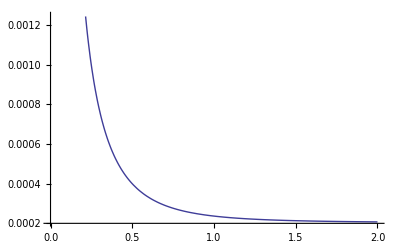

```mathematica
Plot[H[x],{x,0.0001,2}]
```